```mathematica
**This is a program which provides bifurcation Diagrams with respect to any coordinate in an n-dimensional Map. It provides two main functions "ShowAttractor" and "ShowBifurcationDiagram".**
```

```mathematica
$MaxExtraPrecision = 1000000;

TransientPoint[fTP_,initcondTP_,μTP_,transTP_]:=Nest[fTP[#,μTP]&,initcondTP,Round[transTP]];

PointsList[fPL_,initcondPL_,μPL_,npointsPL_]:=NestList[fPL[#,μPL]&,initcondPL,Round[npointsPL]];

ShowAttractor[fSA_,initcondSA_,μSA_,transSA_,npointsSA_,optionsSA_:{{1,2},AxesLabel->{"First Variable","Second Variable"}}]:=Module[{iSA,jSA,x0SA,tableSA,plotSA},x0SA=TransientPoint[fSA,initcondSA,μSA,transSA];tableSA=PointsList[fSA,x0SA,μSA,npointsSA];plotSA=Table[ToExpression[FromCharacterCode[{iSA,65,108,105}]],{iSA,97,96+Length[optionsSA]}];For[jSA=1,jSA<=Length[optionsSA],plotSA[[jSA]]=ListPlot[Table[{tableSA[[iSA,optionsSA[[jSA,1,1]]]],tableSA[[iSA,optionsSA[[jSA,1,2]]]]},{iSA,1,Length[tableSA]}],Rest[optionsSA[[jSA]]]];jSA++];plotSA];

BifurcationTable[fBT_,initcondBT_,transBT_,npointsBT_,{paraMinBT_,paraMaxBT_,nparaBT_:1000}]:=Module[{iBT,pBT,dpBT,x0BT,tableBT},tableBT={};dpBT=(paraMaxBT-paraMinBT)/Round[nparaBT];x0BT=initcondBT;For[iBT=1,iBT<=Round[nparaBT],pBT=paraMinBT+iBT dpBT;x0BT=TransientPoint[fBT,x0BT,pBT,transBT];tableBT=Append[tableBT,{pBT,PointsList[fBT,x0BT,pBT,npointsBT]}];x0BT=Last[Last[Last[tableBT]]];iBT++];tableBT];

ShowBifurcationDiagram[fSBD_,initcondSBD_,transSBD_,npointsSBD_,{paraMinSBD_,paraMaxSBD_,nparaSBD_:1000},optionsSBD_:{1,AxesLabel->{"Parameter Axis","Variable Axis"}}]:=Module[{iSBD,jSBD,kSBD,tableSBD,t1SBD,plotSBD},t1SBD={};tableSBD=BifurcationTable[fSBD,initcondSBD,transSBD,npointsSBD,{paraMinSBD,paraMaxSBD,nparaSBD}];plotSBD=Table[ToExpression[FromCharacterCode[{iSBD,65,108,105}]],{iSBD,97,96+Length[optionsSBD]}];For[jSBD=1,jSBD<=Length[optionsSBD],For[kSBD=1,kSBD<=Length[tableSBD[[1,2]]],t1SBD=Join[t1SBD,Table[{tableSBD[[iSBD,1]],tableSBD[[iSBD,2,kSBD,optionsSBD[[jSBD,1]]]]},{iSBD,1,Length[tableSBD]}]];kSBD++];plotSBD[[jSBD]]=ListPlot[t1SBD,Rest[optionsSBD[[jSBD]]]];t1SBD={};jSBD++];plotSBD];
```

```mathematica
Clear[r,c,x,y,n]
```

```mathematica
f[x_,y_]:=r x(1-x)+c y
g[x_,y_]:= c(x+y);
```

```mathematica
,,,,,,,,,,,,,,,,,,,,,,,,,,,
```

```mathematica
Clear[c,r,x,y]
```

```mathematica
c=0.08;
```

```mathematica
Climate[var_,rpara_]:={rpara var[[1]](1-var[[1]])+c var[[2]],c(var[[1]]+var[[2]])};
```

```mathematica
**We use the function "ShowBifurcationDiagram[the map's head (Name),the initial condition,the transient length,the number of vertical points to be plotted for each parameter value,{the minimum parameter's value, the maximum parameter's value, the number of parameters' values to be considered in this interval},the options for the plots which must be in the form {{i,plot options for this diagram},...,{j,plot options for this diagram}} where i and j are integers between 1 and n (the dimension of the map). To show all the plots we have to put the options as {{1,plot options},{2,plot options},...,{n,plot options}}. But to show one plot only, like for the second coordinate the options should be {{2,Plot options}}]". This function will have graphics array value after executing it of length equal to the number of plots we wanted to draw which we specified it earlier in the options, which can be stored in other variable for manipulation of the graph after wards... where you don't need to excecute the function again with new plot options in order to manipulate the diagram and add other options to it like PlotLabel or any other one.We store the graph which is resulted from this function in a variable named Figure1, as follows**
```

```mathematica
Byfurcation by varying r:
```

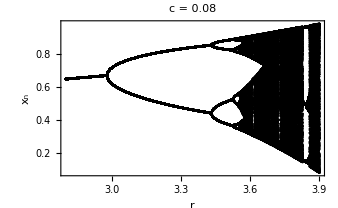
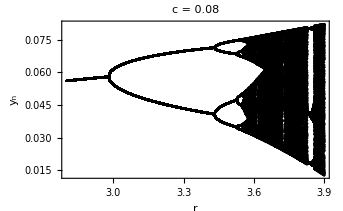

```mathematica
Figure1=ShowBifurcationDiagram[Climate,{0.5,0.1},1000,300,{2.8,3.9,500},{{1,Frame->True,FrameLabel->{StyleForm[" r ", FontSize->12],StyleForm[" x_n ", FontSize->12]},PlotRange->All,Axes->False,PlotStyle->{PointSize[0.005],Black},PlotLabel->" c = 0.08"},{2,Frame->True,FrameLabel->{StyleForm[" r ", FontSize->12],StyleForm[" y_n ", FontSize->12]},PlotRange->All,Axes->False,PlotStyle->{PointSize[0.005],Black},PlotLabel->" c = 0.08"}}]
```

```mathematica
.....................................
```